# VE401 Recitation 1

## About me

```mathematica
me=-Graphics-;
box=FindFaces[me];
HighlightImage[me,box]
```

-Graphics-

Name: GU Zhenhao

QQ: 1742165957

WeChat: GaryGZH (or you can find me in the WeChat group)

E-mail/Zoom: guzhenhao1@sjtu.edu.cn

Asking questions via Piazza is preferred!

## Introduction to Probability and Counting

### Events and Mutually Exclusive Events

Intuition: Events are any subset of the sample space S. Events A_1 and A_2 are mutually exclusive if they cannot be true at the same time.

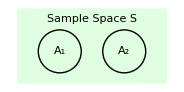

```mathematica
c = LightGreen; (* background color *)
Graphics[{c,Rectangle[{-2,-1.5},{5,2}],Black,Circle[{3,0}],Circle[],Text["A_1",{0,0},Background->c],Text["A_2",{3,0},Background->c],Text["Sample Space S",{1.5,1.5},Background->c]}]
```

Mathematical representation: A_1∩A_2=∅.

### Cardano’s Principle and Tree Diagrams

Intuition: The probability of an outcome A is the proportion of the ways that can lead to A, given that all the ways are equally likely and mutually exclusive.

Mathematical representation:

P[A]=(Number of ways leading to outcome A)/(Number of ways experiment can proceed)

Example: Tossing two (unbiased) coins, P[getting one head]=2/4=0.5.

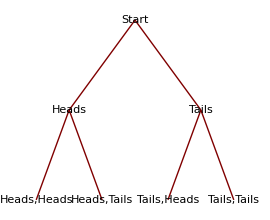

```mathematica
g={"Start"->"Heads","Start"->"Tails","Heads"->"Heads,Heads","Heads"->"Heads,Tails","Tails"->"Tails,Heads","Tails"->"Tails,Tails"};
TreePlot[g,VertexLabeling->True]
```

### Counting

The number of ways leading to outcomes is calculated using the following: with a set A={a_1,a_2,...,a_n} with n objects,

Ways of picking an object k times, allowing repetition: n^k.

Ways of choosing ordered k objects from A: (n!)/((n-k)!).

Ways of choosing unordered k objects from A: (n!)/(k!(n-k)!).

Ways of partitioning A into k subsets, A_1,...,A_k, with the number in the i^th subset is n_i: (n!)/(n_1!n_2!...n_k!).

Example:

##### Tossing a coin 4 times, what is the number of all possible outcomes?

A={heads, tails}, n=2. Total possible outcomes: 2^4=16.

##### Rolling 10 four-sided dice, what is the number of ways of getting 3 ones, 2 twos, 4 threes and 1 four?

A={1^st dice,2^nd dice,...,10^th dice} . We want to divide A into 4 subsets A_1:= dice with rolling result 1, A_2:= dice with rolling result 2, and same for A_3,A_4. In our case we need |A_1|=3, |A_2|=2, |A_3|=4, |A_4|=1, then the number of total possible ways:

```mathematica
(10!)/(3!2!4!1!)
```

12600

### σ-Field

Purpose: To deal with uncountable sample space. We take a family of subsets ℱ on S such that

∅∈ℱ,

If A∈ℱ then S\A∈ℱ,

if A_1,A_2,...∈ℱ is a countable sequence of events, then ∪_k A_k∈ℱ.

### Probability Measures & Spaces

Paraphrase: If a function P wants to be a probability measure, it needs to

map an event to its probability, which is in [0,1],

map the whole sample (event) space to 1, i.e. P[S]=1,

For mutually exclusive events A_1,...,A_k, P[A_1∪A_2∪...∪A_k]=P[A_1]+P[A_2]+...+P[A_k].

Properties:

P[S]=1,

P[∅]=0,

P[S\A]=1-P[A],

P[A_1∪A_2]=P[A_1]+P[A_2]-P[A_1∩A_2].

### Conditional Probability

Intuition: Given A_2 is true, the probability of A_1 is also true is the conditional probability P[A_1|A_2]. We are basically finding where A_1 is true inside the A_2 circle.

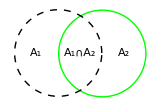

```mathematica
Graphics[{Green,Thick,Circle[{1,0}],Black,Thin,Dashed,Circle[],Text["A_1",{-0.5,0}],Text["A_2",{1.5,0}],Text["A_1∩A_2",{0.5,0}]}]
```

Mathematical representation:

P[A_1|A_2]=P[A_1∩A_2]/P[A_2]
(P[A_1|A_2]P[A_2])/P[A_1]=P[A_2|A_1]

### Independence

Intuition: Events A and B are independent if outcome of A does not effect outcome of B, and vice versa.

Mathematical representation:

P[A|B]=P[A]          if P[B]≠0
P[B|A]=P[B]          if P[A]≠0
P[A∩B]=P[A]P[B]     (Why?)

Summary: given events A and B, what happens to P[A∩B],P[A∪B],P[A|B],P[A|¬B] , and P[¬A|B]? You are encouraged to fill out this table by yourself first.

A and B are ... | mutually exclusive | independent
P[A∩B] |   |  
P[A∪B] |   |  
P[A|B] |   |  
P[A|¬B] |   |  
P[¬A|B] |   |

##### What does this table imply?

A and B are ... | mutually exclusive | independent
P[A∩B] | 0 | P[A]P[B] 
P[A∪B] | P[A]+P[B] | P[A]+P[B]-P[A]P[B] 
P[A|B] | 0 |  P[A]
P[A|¬B] |  P[A]/(1-P[B]) |  P[A]
P[¬A|B] | 1 | 1-P[A]

This table means if events of zero probability are excluded, mutually exclusive events are not independent and independent events are not mutually exclusive.

### Total Probability

Purpose: To write down a probability using the sum of conditional probabilities.

Mathematical representation:

P[B]=∑_(j=1)^n P[B|A_j]P[A_j]          if A_1... A_n⊂S are mutually exclusive and A_1∪...∪A_n=S

### Bayes’s Theorem

Purpose: To switch sides of a conditional probability, i.e. from P[A|B] to P[B|A].

Mathematical representation:

P[A_k|B]=P[B∩A_k]/P[B]=(P[B|A_k]P[A_k])/(P[B|A_k]P[A_k]+P[B|¬A_k]P[¬A_k])

Furthermore, if A_1... A_n⊂S are mutually exclusive and A_1∪...∪A_n=S,

P[A_k|B]=(P[B|A_k]P[A_k])/(∑_(j=1)^n P[B|A_j]P[A_j])

Example: I will recommend this video https://www.youtube.com/watch?v=HZGCoVF3YvM, which gives a nice visualization of Bayes’s theorem.

## Discrete Random Variable

### Discrete Random Variable and Probability Density Function (PDF)

A discrete random variable X maps the sample space to a countable subset Ω of ℝ, with each number representing an event, and the probability density function f_X maps the subset to its probability. The PDF must follow

f_X(x)>0 for all x.

∑_(x∈Ω) f_X(x)=1.

Note: For various distribution of random variable X, we need to know its

parameter(s),

E[X],

Var[X],

probability density function (PDF),

cumulative distribution function (CDF),

moment generating function (MGF), and

when to use it?

### Expectation

Intuition: Given a distribution, what would I expect a random sample to be closest to?

Mathematical representation: for discrete random variable, E[X]=μ_X=μ=∑_(x∈Ω) x f_X(x).

Properties: for any random variable X and Y,

For a constant c∈ℝ, E[c]=c,E[c X]=c E[X],

E[X+Y]=E[X]+E[Y],

For any function φ:Ω→ℝ, E[φ∘X]=∑_(x∈Ω) φ(x) f_X(x).

##### What do these properties imply?

E[·] is a linear operation!

### Variance and Standard Variance

Intuition: how much does random variable deviate from the mean?

Mathematical representation:

Variance: Var[X]=σ_X^2=σ^2=E[(X-E[X])]^2=E[X^2]-E[X]^2.

Standard variance: σ_X=√Var[X].

Properties:

For a constant c∈ℝ, Var[c]=0,Var[c X]=c^2 Var[X].

For independent random variable X and Y, Var[X+Y]=Var[X]+Var[Y].

### Moment and Moment Generating Function (MGF)

Intuition: MGF encodes the sequence of all moments, E[X^0],E[X^1],E[X^2],... into one function.

Mathematical representation: MGF exists iff E[e^(t X)] exists, in which case

m_X(t)=∑_(k=0)^∞ E[X^k]/(k!)t^k=E[e^(t X)]

and the k^th moment can be calculated using E[X^k]=((d^k m_X(t))/(d t^k))_(t=0) .

Properties: Assume MGF exists,

if two distributions have same MGF, then two distributions are identical.

For any constant α,β∈ℝ, m_(α X+β)(t)=e^(β t)m_X(α t).

For independent random variable X_1,X_2, m_(X_1+X_2)=m_X_1 m_X_2.

### Cumulative Distribution Function (CDF)

Mathematical representation: F_X(x):=P[X≤x]=∑_(y≤x) f_X(y).

### Bernoulli Distribution

Purpose: the probability of success in 1 trial?

Parameter and properties:

p∈[0,1], describing the probability of success. q:=1-p.

E[X] | Var[X] | PDF | CDF | MGF
p | p q | Piecewise[{{q, x==0}, {p, x==1}, {0, otherwise}}] | Piecewise[{{0, x<0}, {q, 0≤x<1}, {1, otherwise}}] | q+e^t p

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BernoulliDistribution[p],x],{x,0,1},
PlotRange->{0,1},
AxesOrigin->{-.1,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Bernoulli Distribution with p="<>ToString[p]
],{p,0,1},Paneled->False]
```

### Binomial Distribution

Purpose: how many successes in n trial(s)?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial. q:=1-p.

n∈{0,1,2,...} is the number of trials.

E[X] | Var[X] | PDF | MGF
n p | n p q | Piecewise[{{Binomial[n, x] p^x q^(n-x), 0≤x≤n}, {0, otherwise}}] | (p (e^t-1)+1)^n

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BinomialDistribution[n,p],x],{x,0,n},
PlotRange->{0,1},
AxesOrigin->{-0.1 n,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of Binomial Distribution with p="<>ToString[p]<>", n="<>ToString[n]
],{p,0,1},{n,{1,5,10,15,20}},Paneled->False]
```

### Geometric Distribution

Purpose: how many trials until first success?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial. q:=1-p.

E[X] | Var[X] | PDF | CDF | MGF
1/p | q/p^2 | Piecewise[{{q^(x-1) p, x≥1}, {0, otherwise}}] | Piecewise[{{1-q^Floor[x], x≥1}, {0, otherwise}}] | (p e^t)/(1-q e^t)

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[GeometricDistribution[p],x-1],{x,1,10},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)"},
ImageSize->300,
PlotLabel->"PDF of Geometric Distribution with p="<>ToString[p]
],{p,0.001,1},Paneled->False]
```

### Hypergeometric Distribution

Purpose: Select n samples from N objects (within which r objects have trait), what is the probability of having x objects with trait?

Parameter and properties:

N∈{0,1,2,...} is the number of total objects.

n∈{0,1,2,...,N} is the number of samples.

r∈{0,1,2,...,N} is the number of objects with traits. p:=r/N,q:=1-p.

E[X] | Var[X] | PDF
n p | n p q (N-n)/(N-1) | Piecewise[{{(Binomial[r, x] Binomial[N-r, n-x])/Binomial[N, n], 0≤x≤N}, {0, otherwise}}]

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[HypergeometricDistribution[Floor[n*Ν],Floor[r*Ν],Ν],x],{x,1,Ν},
PlotRange->{0,1},
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Hypergeometric Distribution with N="<>ToString[Ν]<>", r="<>ToString[Floor[r*Ν]]<>", n="<>ToString[Floor[n*Ν]]
],{Ν,{5,10,50,100}},{n,0,1},{r,0,1},Paneled->False]
```

Approximation: if n/N is sufficiently small, it can be approximated by binomial distribution with parameter n and p=r/N.

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
{PDF[HypergeometricDistribution[Floor[n*Ν],Floor[r*Ν],Ν],x],PDF[BinomialDistribution[Floor[n*Ν],Floor[r*Ν]/Ν],x]},{x,1,Ν},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of two distributions",
PlotLegends->{"Hypergeometric distribution\n with N="<>ToString[Ν]<>", r="<>ToString[Floor[r*Ν]]<>", n="<>ToString[Floor[n*Ν]],"Binomial distribution\n with n="<>ToString[Floor[n*Ν]]<>", p="<>ToString[N[Floor[r*Ν]/Ν]]}
],{Ν,{5,10,50,100}},{n,0,1},{r,0,1},Paneled->False]
```

### Poisson Distribution

Purpose: how many arrivals in a small time interval?

Parameter and properties:

λ>0, describing the rate of arrival.

Mean | Var[X] | PDF | MGF
λ | λ | Piecewise[{{(e^-λ λ^x)/(x!), x≥0}, {0, otherwise}}] | e^(λ (e^t-1))

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[PoissonDistribution[λ],x],{x,0,10},
PlotRange->{0,1},
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Poisson Distribution with λ="<>ToString[λ]
],{λ,0.001,5},Paneled->False]
```

## Problems For Discussion

### Banach Matchbox Problem

Problem: Suppose a mathematician carries two matchboxes at all times: one in his left pocket and one in his right. Each time he needs a match, he is equally likely to take it from either pocket. Suppose he reaches into his pocket and discovers for the first time that the box picked is empty. If it is assumed that each of the matchboxes originally contained n matches, what is the probability that there are exactly k matches in the other box?

#### Solution

We can set success as picking a match from the matchbox that will eventually become empty, and failure as picking a match from the other box. 
The question then transform to the following: what’s the probability of having n successes in 2n-k trials? It follows immediately that we need to use binomial distribution. The matchbox that will eventually become empty can be either left or right box for equal probability. So,

P[X=k]=(2n-k
n)(1/2)^n(1/2)^(n-k)1/2×2=(2n-k
n)(1/2)^(2n-k)

#### Another Solution

The number of ways of having an empty box and a matchbox with x matches left is (2n-x
n)·2, By Cardano’s Principle,

P[X=k]=((2n-k
n)·2)/(∑_(i=0)^n (2n-i
n)·2)=(2n-k
n)/(∑_(i=0)^n (2n-i
n))

Which one is correct?

### Two Envelopes Problem

Problem: You are given two indistinguishable envelopes, each containing money, one contains twice as much as the other. You may pick one envelope and keep the money it contains. Having chosen an envelope at will, but before inspecting it, you are given the chance to switch envelopes. Should you switch?

#### Solution

Suppose the amount of money in the envelope I choose is x, then the amount in the other envelope is

Piecewise[{{1/2 x, with probability 1/2}, {2x, with probability 1/2}}]

So we expect to get 1/2 x·1/2+2x·1/2=5/4 x>x. So we should switch.

#### Another Solution

Suppose the total amount of money in the two envelopes is x, then the amount in both envelopes is

Piecewise[{{1/3 x, with probability 1/2}, {2/3 x, with probability 1/2}}]

So we expect to get 1/3 x·1/2+2/3 x·1/2=1/2 x, with or without switching. So switching won’t help.
Which one is correct?